```mathematica
(*带电圆环的电场*)
```

```mathematica
Integrate[1/(√(a-b Cos[φ])),{φ,0,2π},Assumptions->a>b>0]
```

1/(√(a^2-b^2))2 (√(a+b) EllipticK[-(2 b)/(a-b)]+√(a-b) EllipticK[(2 b)/(a+b)])

```mathematica
Plot[EllipticK[x],{x,-20,1},AspectRatio->1,PlotRange->{0,10}]
```

-Graphics-

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[z_,ρ_]:=1/(√(a^2-b^2))2 (√(a+b) EllipticK[-(2 b)/(a-b)]+√(a-b) EllipticK[(2 b)/(a+b)]);
Plot3D[V[z,ρ],{z,-3R,3R},{ρ,0,3R},PlotRange->All,PlotPoints->50,AxesLabel->{"z","ρ","V"}]
```

-Graphics3D-

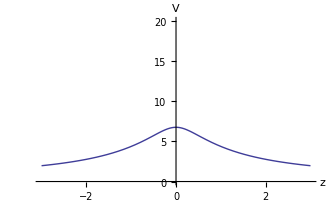

```mathematica
Plot[V[z,ρ]/.ρ->0.5,{z,-3R,3R},PlotRange->{0,20},AxesLabel->{"z","V"}]
```

```mathematica
field=-D[V[z,ρ],z]/.ρ->0;
Plot[field,{z,-3R,3R},AxesLabel->{"z","E_z"}]
```

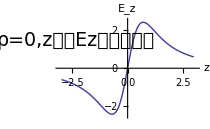

```mathematica
Clear[ρ,field,V,R,a,b]
```

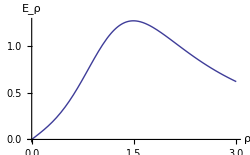

```mathematica
field=-D[V[z,ρ],ρ]/.z->1;
Plot[field,{ρ,0,3R},AxesLabel->{"ρ","E_ρ"}]
```

```mathematica
(*折线法求xoz截面上的场线*)
```

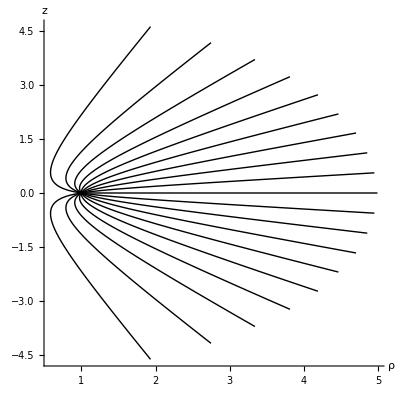

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[ρ_,z_]:=1/(√(a^2-b^2))2 (√(a+b) EllipticK[-(2 b)/(a-b)]+√(a-b) EllipticK[(2 b)/(a+b)])
field=-D[V[ρ,z],ρ]-ⅈ*D[V[ρ,z],z];
step=0.03;r1=0.02;r2=5;forceline={};
Do[θ=ϕ;p0={1,0};single={p0};
Label[ss];p=Last[single];p=p+step*{Cos[θ],Sin[θ]};θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];
If[(Norm[p-p0]≥r1)∧(Norm[p]<r2),AppendTo[single,p];Goto[ss]];AppendTo[forceline,single],{ϕ,-π+π/10,π-π/10,π/10}]
Show[Graphics[{Line/@forceline}],Axes->True,AspectRatio->1,AxesLabel->{"ρ","z"},AxesOrigin->{0,0}]
```

```mathematica
Clear[V,R,a,b,field,step,r1,r2,forceline,θ,p0,p1,p,single,pp]
```